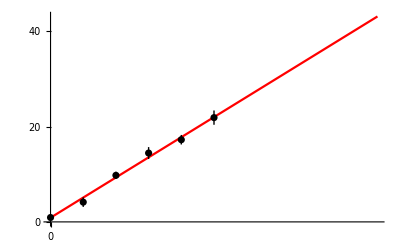

(Parametro | 4.22694 | 0.879203
Incertidumbre | 0.0438811 | 0.202922
E. Porcentual | 1.03813 % | 23.0803 %)

Export Graph.png on Documents

Export Graph.pdf on Documents

Export Parameter Matrix on Documents

```mathematica
dat=Import["D:\\Carpetas de computadora\\Documentos\\Escuela\\Libros\\Programas\\Mathematica\\para el de ajustes.dat"];
x[n_]:=dat[[n,1]];
δx[n_]:=dat[[n,2]];
y[n_]:=dat[[n,3]];
δy[n_]:=dat[[n,4]];
L=Length[dat];
xlist=Array[x,L];
xy[i_]:={Around[x[i],δx[i]],Around[ y[i],δy[i]]};
xylist=Array[xy,L];

m=((-∑_(i=1)^L x[i]/δy[i]^2) ∑_(i=1)^L y[i]/δy[i]^2+(∑_(i=1)^L 1/δy[i]^2) ∑_(i=1)^L (x[i] y[i])/δy[i]^2)/(-(∑_(i=1)^L x[i]/δy[i]^2)^2+(∑_(i=1)^L x[i]^2/δy[i]^2) ∑_(i=1)^L 1/δy[i]^2);
b=((∑_(i=1)^L x[i]^2/δy[i]^2) ∑_(i=1)^L y[i]/δy[i]^2-(∑_(i=1)^L x[i]/δy[i]^2) ∑_(i=1)^L (x[i] y[i])/δy[i]^2)/(-(∑_(i=1)^L x[i]/δy[i]^2)^2+(∑_(i=1)^L x[i]^2/δy[i]^2) ∑_(i=1)^L 1/δy[i]^2);
δm=(∑_(i=1)^L 1/δy[i]^2)/(-(∑_(i=1)^L x[i]/δy[i]^2)^2+(∑_(i=1)^L x[i]^2/δy[i]^2) ∑_(i=1)^L 1/δy[i]^2);
δb=(∑_(i=1)^L x[i]^2/δy[i]^2)/(-(∑_(i=1)^L x[i]/δy[i]^2)^2+(∑_(i=1)^L x[i]^2/δy[i]^2) ∑_(i=1)^L 1/δy[i]^2);
cov=(-∑_(i=1)^L x[i]/δy[i]^2)/(-(∑_(i=1)^L x[i]/δy[i]^2)^2+(∑_(i=1)^L x[i]^2/δy[i]^2) ∑_(i=1)^L y[i]/δy[i]^2);
y[x_]:=m x+ b;
Graph1=Show[Plot[y[x],{x,0,Max[xlist]+5},PlotStyle->Red,AxesStyle->Arrowheads[Automatic],Ticks->{Range[0,110,10],Range[0,110,10]}],ListPlot[xylist,PlotStyle->Black]]
Pmat={{"Parametro",m,b},{"Incertidumbre", δm,δb},{"E. Porcentual",(100*δm)/m"%",(100*δb)/b"%"}};
Pmat//MatrixForm
Button["Export Graph.png on Documents",Export["Graph1.png",Graph1]]
Button["Export Graph.pdf on Documents",Export["Graph1.pdf",Graph1]]
Button["Export Parameter Matrix on Documents",Export["PMatrix.dat",Pmat]]
```